```mathematica
(* Extra Credit Problem *)
(* Fixation of a Mutant Gene *)

(* I found this function at the following link http://www.biology.arizona.edu/biomath/tutorials/Applications/MutantGene01.html *)

(* THE FOLLOWING BLOCK OF TEXT COMES FROM THE LINK PROVIDED ABOVE *)
(* Consider a population of N breeding diploid organisms. Suppose that a new genetic mutation arises in a single gene copy within an individual,producing a new allele A.There is a small probability that the frequency,p,of this mutant allele within the breeding population will increase and become fixed (i.e.p=1;the population eventually becomes monomorphic).In 1969,Japanese geneticists Motoo Kimura and Tomdko Ohta computed the probability of fixation of such a new mutation (under certain assumptions) as, equation:

p=(1-e^-2s)/(1-e^-4Ns).

where s is the selective advantage of allele A and N is the number of breeding individuals[1]. *)

(* We will fix our population n=100,000.  Also, since the function is undefined at s=0 and it approaches 1 quickly as s->, we will restrict our investigation to the closed interval [.1 to 1.9],
and out ten x values will be {.1, .3, .5, .7, .9, 1.1, 1.3, 1.5, 1.7, 1.9} *)
```

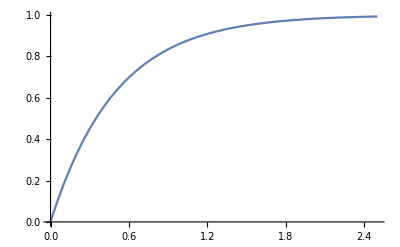

```mathematica
p[s_]:=(1-Exp[-2*s])/(1-Exp[-4*100000*s]);
Plot[p[s],{s,0,2.5}]
```

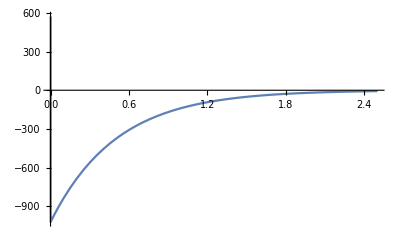

```mathematica
pprime10[s_]=D[p[s],s,s,s,s,s,s,s,s,s,s];
Plot[pprime10[s],{s,0,2.5}]
```

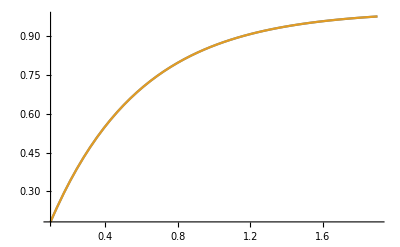

```mathematica
(* generating x values from .1 to 1.9 in increments of 0.2, and then obtaining y values corresponding to x's *)
xval={};
For[i=1,i≤10,++i,
AppendTo[xval,.1+.2*(i-1)]
];

yval={};
For[i=1,i≤10,++i,
AppendTo[yval,p[xval[[i]]]]
]; 

(* Vandermonde Matrix *)

A={};
For[i=1,i≤Length[yval],++i,
inew={};
For[j=1,j≤Length[yval],++j,
AppendTo[inew,xval[[i]]^(j-1)]
];
AppendTo[A,inew]
];
coef=LinearSolve[A,yval];
poly[x_]:=coef.Table[x^i,{i,0,9}];
Plot[{p[x],poly[x]},{x,.1,1.9}]
(* The plot of our function p and the polynomial interpolation superimposed.  Looks good. *)
```

```mathematica
(* Lagrange Polynomials *)
```

```mathematica
fun={};
For[i=1,i≤10,++i,
L[x_]=1;
For[j=1,j≤10,++j,
If[j≠i,
L[x_]=L[x]*(x-xval[[j]])/(xval[[i]]-xval[[j]]),
];
];
AppendTo[fun,L[x]]
];

For[i=1,i≤10,++i,
Subscript[lp, i][x_]=fun[[i]]
];

(* Testing output *)
test={};
For[i=1,i≤10,++i,
irow={};
For[j=1,j≤10,++j,
AppendTo[irow,Subscript[lp, i][xval[[j]]]]
];
AppendTo[test,irow]
];
MatrixForm[test]
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
funq={};
For[i=1,i≤10,++i,
Subscript[q, i][x_]=yval[[i]]*Subscript[lp, i][x];
];
```

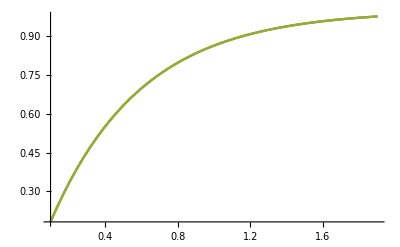

```mathematica
q[x_]=Subscript[q, 1][x];
For[i=2,i≤10,++i,
q[x_]=q[x]+Subscript[q, i][x]
];
Plot[{p[x],q[x],poly[x]},{x,.1,1.9}]
(* The plot of the function p with both the Vandermonde polynomial interpolation and the Lagrange polynomial superimposed. *)
```

```mathematica
(* From the graph of f(10) plotted above, we see that M occurs at the left endpoint of our domain of interest, [0.1, 1.9] *)

M=Abs[pprime10[0.1]];

(* calculating error bound *)
```

```mathematica
errorbound=M/(Length[xval]!)*(1.9-.1)^Length[xval]
```

0.0824903

```mathematica
(* For mean interpolation error, I can not get Mathematica to evaluate the integral of (p[x]-poly[x])^2, or (p[x]-q[x])^2, or even just p[x] on the interval in question.  It just freezes up. I calculated it on MATLAB instead and got 
6.7087*10^-6, so very small *)
```

```mathematica
(* Calculating the derivative of the function p and the polynomial interpolation.  Again, Mathematica will not evaluate the integral for mean interpolation error, so I calculated it on MATLAB.  The mean square error is 1.4626*10^-5, so small, but not as small as mean square error of original functions*)
pprime[x_]=D[p[x],x];
polyprime[x_]=D[poly[x],x];
```

```mathematica
(* Calculating the second derivatives of p and the polynomial interpolation.  Again, calcuating on MATLAB, the mean square error is 2.7789*10^-5, so the mean square error is larger than the previous mean square error for each time we differentiate.  Still, the approximations are pretty good. *)
pprimeprime[x_]=D[p[x],x,x];
polyprimeprime[x_]=D[poly[x],x,x];
```